-Graphics-

WSMSimulate::msg: "[terminate]: came close enough"

WSMSimulate::msg: "Simulation terminated at time 23.8732"

WSMSimulate::term: Simulation of "Attempt" terminated because of a terminate statement.

WSMSimulate::msg: "[terminate]: came close enough"

General::stop: Further output of WSMSimulate :: msg will be suppressed during this calculation.

WSMSimulate::term: Simulation of "Attempt" terminated because of a terminate statement.

General::stop: Further output of WSMSimulate :: term will be suppressed during this calculation.

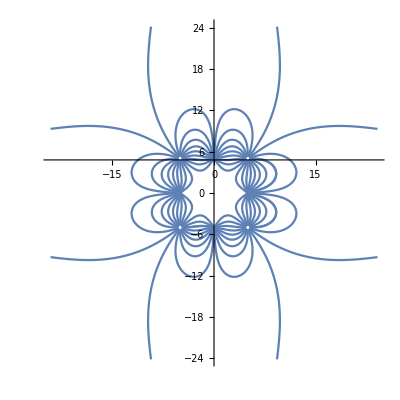

```mathematica
f1[i_]:=DialogInput[DynamicModule[{p={0,0},q = 0},
{Column[{StringJoin[{"Charge ",ToString[i]}],Row[{Column[{Slider2D[Dynamic[p],{{-5,-5},{5,5},{0.5,0.5}}],
Dynamic[p]}],
Column[{TextCell["Charge Value of Charged Particle in Coloumbs"],
InputField[Dynamic[q],Number],
DefaultButton["OK",DialogReturn[{p,q}]]}]}]}]}]];
f2[i_]:=DialogInput[DynamicModule[{n},Column[{"Number of Charged Particles Contributing to Electric Field",InputField[Dynamic[n],Number],DefaultButton["OK",DialogReturn[n]]}]]];
g[i_]:=componentNames[[i]]∈"EFieldLine.Components.CParticle";
h[i_]:=componentNames[[i]]<>".field"-> "tparticle1.E";
j[i_]:=componentNames[[i]]<>".q"-> chargeInfo[[i]][[2]];
k[i_]:=componentNames[[i]]<>".x"-> chargeInfo[[i]][[1]][[1]];
m[i_]:=componentNames[[i]]<>".y"-> chargeInfo[[i]][[1]][[2]];
nCharges=f2[1];
chargeInfo = Table[f1[i],{i,1,nCharges}];
componentNames=Table["c"<>ToString[i],{i,1,nCharges}];
components=Append[Table[g[x],{x,1,nCharges}],"tparticle1" ∈"EFieldLine.Components.TParticle"];
connections=Table[h[x],{x,1,nCharges}];
Needs["WSMLink`"]
Append[components,"tparticle1" ∈"EFieldLine.Components.TParticle"];
model=WSMConnectComponents["Attempt",components,connections]
WSMSetValues[model,Table[j[x],{x,1,nCharges}]];
WSMSetValues[model,Table[k[x],{x,1,nCharges}]];
WSMSetValues[model,Table[m[x],{x,1,nCharges}]];
createStartPoints[x0_,y0_,r_,n_]:=Table[{r*Cos[theta]+x0,r*Sin[theta]+y0},{theta,0,2*Pi,2*Pi/n}];
singleEfieldLineSim[{x0_, y0_}]:= WSMSimulate["Attempt", {0,100},WSMParameterValues->{"tparticle1.x0"->{x0},"tparticle1.y0"->{y0}}];
multipleEfieldLineSims[x0_,y0_,r_,n_]:=Map[singleEfieldLineSim,createStartPoints[x0,y0,r,n]];
dmR1SimTime[i_]:=mR1[[i]]["SimulationInterval"][[2]];
results=Table[1,{l,1,nCharges}];
EpPlot[i_]:=ParametricPlot[{xR1[[i]][t],yR1[[i]][t]},{t,0,dmR1SimTime[i]}];
For[i=1,i≤nCharges,i++,mR1 = multipleEfieldLineSims[chargeInfo[[i]][[1]][[1]],chargeInfo[[i]][[1]][[2]],0.25,20];
yR1=Table[mR1[[x]]["tparticle1.y"],{x,1,Dimensions[mR1][[1]]}];
xR1=Table[mR1[[y]]["tparticle1.x"],{y,1,Dimensions[mR1][[1]]}];
results[[i]]=Table[EpPlot[z],{z,1,Dimensions[mR1][[1]]}]];
Show[results,PlotRange->All]
```

```mathematica
Show[%244,ImageSize->Full]
```

-Graphics-

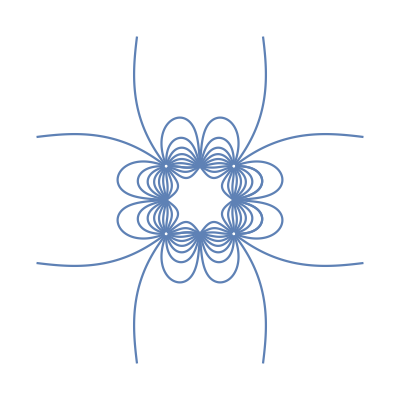

```mathematica
Show[%249,Axes->False]
```

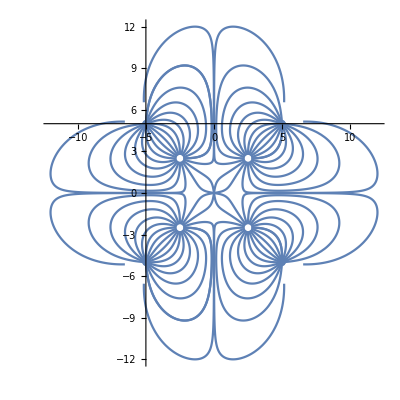

```mathematica
Show[%217,ImageSize->Full]
```

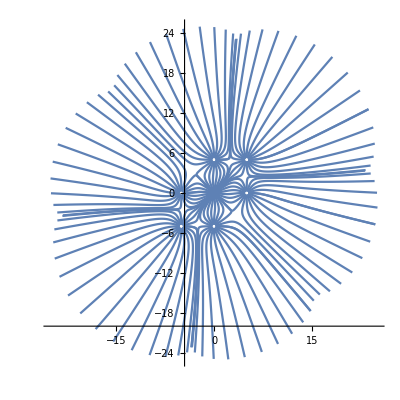

```mathematica
Show[%190,ImageSize->Full]
```

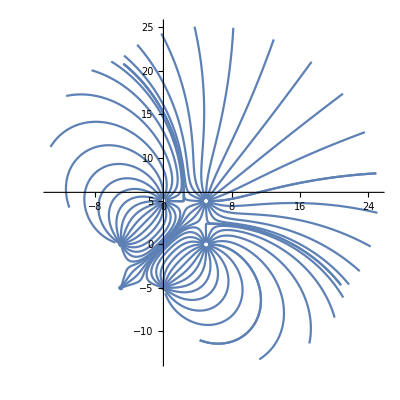

```mathematica
Show[%163,ImageSize->Full]
```

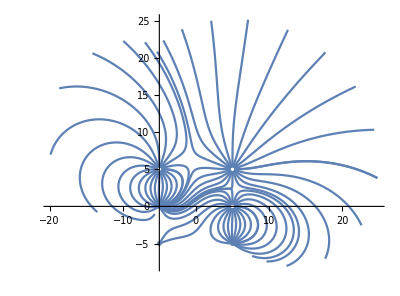

```mathematica
Show[%136,ImageSize->Full]
```

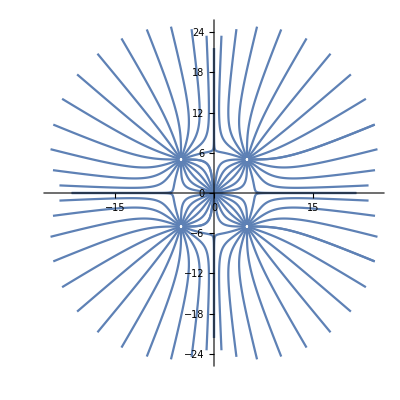

```mathematica
Show[%109,ImageSize->Full]
```

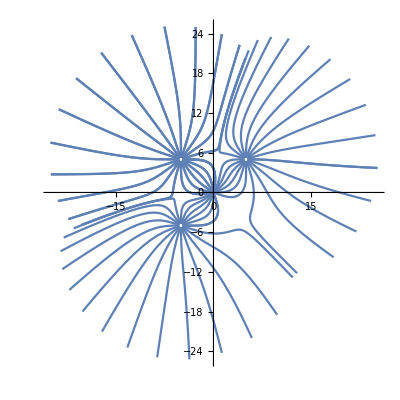

```mathematica
Show[%82,ImageSize->Full]
```

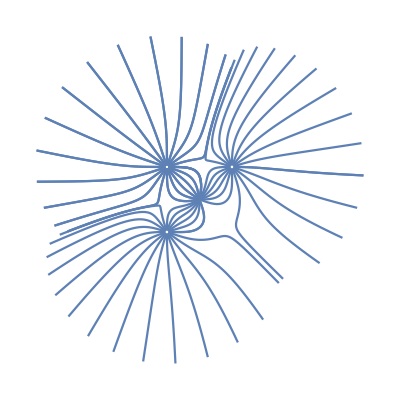

```mathematica
Show[%247,Axes->False]
```

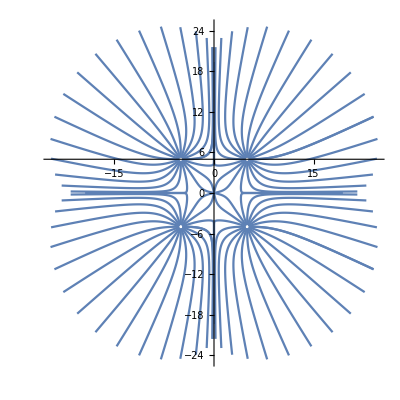

```mathematica
Show[%53,ImageSize->Full]
```

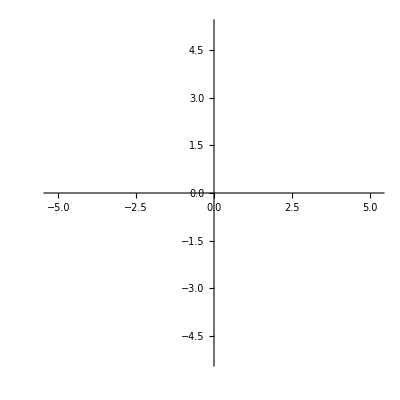

```mathematica
Show[%26,ImageSize->Full]
```